```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/exptail_GW/math"];
```

```mathematica
Zcc=Re[Import["C_and_Z_plot/OGW_Ztermcrcr_005.dat"]//ToExpression];
Ccc=Re[Import["C_and_Z_plot/OGW_Ctermcrcr_005.dat"]//ToExpression];
```

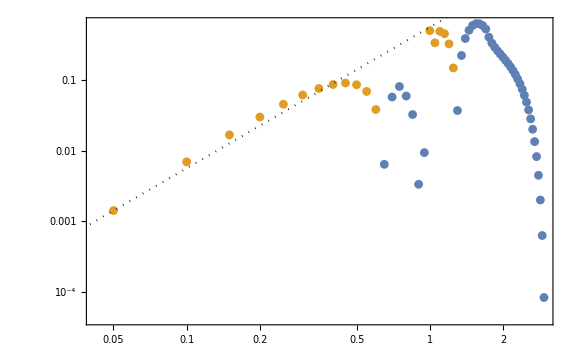

```mathematica
Show[ListLogLogPlot[{Zcc,Zcc.{{1,0},{0,-1}}},Joined->False],LogLogPlot[-Zcc[[1,2]](k/Zcc[[1,1]])^2,{k,0.04,10},PlotStyle->{Black,Dotted}]]
```

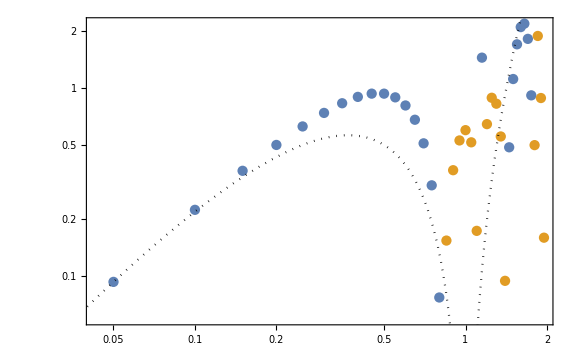

```mathematica
Show[ListLogLogPlot[{Ccc,Ccc.{{1,0},{0,-1}}},Joined->False],LogLogPlot[Ccc[[1,2]]((k Log[k])/(Ccc[[1,1]]Log[Ccc[[1,1]]]))^2,{k,0.04,10},PlotStyle->{Black,Dotted}]]
```

```mathematica
$Assumptions={ks>0,k>0,q>0,0<q/(2ks)<1,-1<(q^2+k^2-ks^2)/(2q k)<1,0<ck^2<1,0<c2^2<1,0<c3p^2<1};
```

```mathematica
RθkT={{Cos[θk],0,-Sin[θk]},{0,1,0},{Sin[θk],0,Cos[θk]}};RθkT//MatrixForm
RϕkT={{Cos[ϕk],Sin[ϕk],0},{-Sin[ϕk],Cos[ϕk],0},{0,0,1}};RϕkT//MatrixForm
Rϕk=Transpose[RϕkT];Rϕk//MatrixForm
```

(Cos[θk] | 0 | -Sin[θk]
0 | 1 | 0
Sin[θk] | 0 | Cos[θk])

(Cos[ϕk] | Sin[ϕk] | 0
-Sin[ϕk] | Cos[ϕk] | 0
0 | 0 | 1)

(Cos[ϕk] | -Sin[ϕk] | 0
Sin[ϕk] | Cos[ϕk] | 0
0 | 0 | 1)

```mathematica
kk=k Transpose[{{Sin[θk]Cos[ϕk],Sin[θk]Sin[ϕk],Cos[θk]}}];
```

```mathematica
Rϕk.RθkT.RϕkT.kk//Simplify
```

{{0},{0},{k}}

```mathematica
qq1=Transpose[{{q1x,q1y,q1z}}];
qq2=Transpose[{{q2x,q2y,q2z}}];
qq3=Transpose[{{q3x,q3y,q3z}}];
qq=qq1+qq2-qq3;
qq3p=qq3-qq2;
```

```mathematica
coord1=Join[Flatten[qq1],Flatten[qq2],Flatten[qq3]]
coord2=Join[Flatten[qq],Flatten[qq2],Flatten[qq3p]]
```

{q1x,q1y,q1z,q2x,q2y,q2z,q3x,q3y,q3z}

{q1x+q2x-q3x,q1y+q2y-q3y,q1z+q2z-q3z,q2x,q2y,q2z,-q2x+q3x,-q2y+q3y,-q2z+q3z}

```mathematica
JJ=Table[D[coord2[[i]], coord1[[j]]],{i,9},{j,9}]//Simplify
```

{{1,0,0,1,0,0,-1,0,0},{0,1,0,0,1,0,0,-1,0},{0,0,1,0,0,1,0,0,-1},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,-1,0,0,1,0,0},{0,0,0,0,-1,0,0,1,0},{0,0,0,0,0,-1,0,0,1}}

```mathematica
Det[JJ]
```

1

```mathematica
qq=q Transpose[{{0,0,1}}];
qq2=q2 Transpose[{{Sin[θ2]Cos[ϕ2],Sin[θ2]Sin[ϕ2],Cos[θ2]}}];
qq3p=q3p Transpose[{{Sin[θ3p]Cos[ϕ3p],Sin[θ3p]Sin[ϕ3p],Cos[θ3p]}}];
```

```mathematica
qqt=Rϕk.RθkT.RϕkT.qq/.{Cos[θk]->ck,Sin[θk]->Sqrt[1-ck^2],Cos[θ2]->c2,Sin[θ2]->Sqrt[1-c2^2],Cos[θ3p]->c3p,Sin[θ3p]->Sqrt[1-c3p^2]}//Simplify
qq2t=Rϕk.RθkT.RϕkT.qq2/.{Cos[θk]->ck,Sin[θk]->Sqrt[1-ck^2],Cos[θ2]->c2,Sin[θ2]->Sqrt[1-c2^2],Cos[θ3p]->c3p,Sin[θ3p]->Sqrt[1-c3p^2]}//Simplify
qq3pt=Rϕk.RθkT.RϕkT.qq3p/.{Cos[θk]->ck,Sin[θk]->Sqrt[1-ck^2],Cos[θ2]->c2,Sin[θ2]->Sqrt[1-c2^2],Cos[θ3p]->c3p,Sin[θ3p]->Sqrt[1-c3p^2]}//Simplify
```

{{-√(1-ck^2) q Cos[ϕk]},{-√(1-ck^2) q Sin[ϕk]},{ck q}}

{{q2 (-c2 √(1-ck^2) Cos[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕk] Sin[ϕ2] Sin[ϕk]+√(1-c2^2) Cos[ϕ2] (ck Cos[ϕk]^2+Sin[ϕk]^2))},{q2 (-c2 √(1-ck^2) Sin[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕ2] Cos[ϕk] Sin[ϕk]+√(1-c2^2) Sin[ϕ2] (Cos[ϕk]^2+ck Sin[ϕk]^2))},{q2 (c2 ck+√(1-c2^2) √(1-ck^2) Cos[ϕ2-ϕk])}}

{{q3p (-c3p √(1-ck^2) Cos[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕk] Sin[ϕ3p] Sin[ϕk]+√(1-c3p^2) Cos[ϕ3p] (ck Cos[ϕk]^2+Sin[ϕk]^2))},{q3p (-c3p √(1-ck^2) Sin[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕ3p] Cos[ϕk] Sin[ϕk]+√(1-c3p^2) Sin[ϕ3p] (Cos[ϕk]^2+ck Sin[ϕk]^2))},{q3p (c3p ck+√(1-c3p^2) √(1-ck^2) Cos[ϕ3p-ϕk])}}

```mathematica
xcoord=Join[Flatten[qqt],Flatten[qq2t],Flatten[qq3pt]]
rcoord={q,ck,ϕk,q2,c2,ϕ2,q3p,c3p,ϕ3p}
```

{-√(1-ck^2) q Cos[ϕk],-√(1-ck^2) q Sin[ϕk],ck q,q2 (-c2 √(1-ck^2) Cos[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕk] Sin[ϕ2] Sin[ϕk]+√(1-c2^2) Cos[ϕ2] (ck Cos[ϕk]^2+Sin[ϕk]^2)),q2 (-c2 √(1-ck^2) Sin[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕ2] Cos[ϕk] Sin[ϕk]+√(1-c2^2) Sin[ϕ2] (Cos[ϕk]^2+ck Sin[ϕk]^2)),q2 (c2 ck+√(1-c2^2) √(1-ck^2) Cos[ϕ2-ϕk]),q3p (-c3p √(1-ck^2) Cos[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕk] Sin[ϕ3p] Sin[ϕk]+√(1-c3p^2) Cos[ϕ3p] (ck Cos[ϕk]^2+Sin[ϕk]^2)),q3p (-c3p √(1-ck^2) Sin[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕ3p] Cos[ϕk] Sin[ϕk]+√(1-c3p^2) Sin[ϕ3p] (Cos[ϕk]^2+ck Sin[ϕk]^2)),q3p (c3p ck+√(1-c3p^2) √(1-ck^2) Cos[ϕ3p-ϕk])}

{q,ck,ϕk,q2,c2,ϕ2,q3p,c3p,ϕ3p}

```mathematica
JJ=Table[D[xcoord[[i]], rcoord[[j]]],{i,9},{j,9}]//FullSimplify
```

{{-√(1-ck^2) Cos[ϕk],(ck q Cos[ϕk])/(√(1-ck^2)),√(1-ck^2) q Sin[ϕk],0,0,0,0,0,0},{-√(1-ck^2) Sin[ϕk],(ck q Sin[ϕk])/(√(1-ck^2)),-√(1-ck^2) q Cos[ϕk],0,0,0,0,0,0},{ck,q,0,0,0,0,0,0,0},{0,q2 ((c2 ck)/(√(1-ck^2))+√(1-c2^2) Cos[ϕ2-ϕk]) Cos[ϕk],q2 (√(1-c2^2) (-1+ck) Sin[ϕ2-2 ϕk]+c2 √(1-ck^2) Sin[ϕk]),-c2 √(1-ck^2) Cos[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕk] Sin[ϕ2] Sin[ϕk]+√(1-c2^2) Cos[ϕ2] (ck Cos[ϕk]^2+Sin[ϕk]^2),-(q2 (c2 (1+ck) Cos[ϕ2]+c2 (-1+ck) Cos[ϕ2-2 ϕk]+2 √(1-c2^2) √(1-ck^2) Cos[ϕk]))/(2 √(1-c2^2)),-1/2 √(1-c2^2) q2 ((1+ck) Sin[ϕ2]+(-1+ck) Sin[ϕ2-2 ϕk]),0,0,0},{0,q2 ((c2 ck)/(√(1-ck^2))+√(1-c2^2) Cos[ϕ2-ϕk]) Sin[ϕk],q2 (√(1-c2^2) (-1+ck) Cos[ϕ2-2 ϕk]-c2 √(1-ck^2) Cos[ϕk]),1/2 √(1-c2^2) ((1+ck) Sin[ϕ2]-(-1+ck) Sin[ϕ2-2 ϕk])-c2 √(1-ck^2) Sin[ϕk],-(q2 (c2 (1+ck) Sin[ϕ2]-c2 (-1+ck) Sin[ϕ2-2 ϕk]+2 √(1-c2^2) √(1-ck^2) Sin[ϕk]))/(2 √(1-c2^2)),1/2 √(1-c2^2) q2 ((1+ck) Cos[ϕ2]-(-1+ck) Cos[ϕ2-2 ϕk]),0,0,0},{0,q2 (c2-(√(1-c2^2) ck Cos[ϕ2-ϕk])/(√(1-ck^2))),√(1-c2^2) √(1-ck^2) q2 Sin[ϕ2-ϕk],c2 ck+√(1-c2^2) √(1-ck^2) Cos[ϕ2-ϕk],q2 (ck-(c2 √(1-ck^2) Cos[ϕ2-ϕk])/(√(1-c2^2))),-√(1-c2^2) √(1-ck^2) q2 Sin[ϕ2-ϕk],0,0,0},{0,q3p ((c3p ck)/(√(1-ck^2))+√(1-c3p^2) Cos[ϕ3p-ϕk]) Cos[ϕk],q3p (√(1-c3p^2) (-1+ck) Sin[ϕ3p-2 ϕk]+c3p √(1-ck^2) Sin[ϕk]),0,0,0,-c3p √(1-ck^2) Cos[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕk] Sin[ϕ3p] Sin[ϕk]+√(1-c3p^2) Cos[ϕ3p] (ck Cos[ϕk]^2+Sin[ϕk]^2),-(q3p (c3p (1+ck) Cos[ϕ3p]+c3p (-1+ck) Cos[ϕ3p-2 ϕk]+2 √(1-c3p^2) √(1-ck^2) Cos[ϕk]))/(2 √(1-c3p^2)),-1/2 √(1-c3p^2) q3p ((1+ck) Sin[ϕ3p]+(-1+ck) Sin[ϕ3p-2 ϕk])},{0,q3p ((c3p ck)/(√(1-ck^2))+√(1-c3p^2) Cos[ϕ3p-ϕk]) Sin[ϕk],q3p (√(1-c3p^2) (-1+ck) Cos[ϕ3p-2 ϕk]-c3p √(1-ck^2) Cos[ϕk]),0,0,0,1/2 √(1-c3p^2) ((1+ck) Sin[ϕ3p]-(-1+ck) Sin[ϕ3p-2 ϕk])-c3p √(1-ck^2) Sin[ϕk],-(q3p (c3p (1+ck) Sin[ϕ3p]-c3p (-1+ck) Sin[ϕ3p-2 ϕk]+2 √(1-c3p^2) √(1-ck^2) Sin[ϕk]))/(2 √(1-c3p^2)),1/2 √(1-c3p^2) q3p ((1+ck) Cos[ϕ3p]-(-1+ck) Cos[ϕ3p-2 ϕk])},{0,q3p (c3p-(√(1-c3p^2) ck Cos[ϕ3p-ϕk])/(√(1-ck^2))),√(1-c3p^2) √(1-ck^2) q3p Sin[ϕ3p-ϕk],0,0,0,c3p ck+√(1-c3p^2) √(1-ck^2) Cos[ϕ3p-ϕk],q3p (ck-(c3p √(1-ck^2) Cos[ϕ3p-ϕk])/(√(1-c3p^2))),-√(1-c3p^2) √(1-ck^2) q3p Sin[ϕ3p-ϕk]}}

```mathematica
Det[JJ]//Simplify
```

-q^2 q2^2 q3p^2

```mathematica
ep={{1,0,0},{0,-1,0},{0,0,0}};
ec={{0,1,0},{1,0,0},{0,0,0}};
Tr[ep]
Tr[ec]
```

0

0

```mathematica
pp=Transpose[{{px,py,pz}}];
```

```mathematica
Transpose[pp].ep.pp
Transpose[pp].ec.pp
```

{{px^2-py^2}}

{{2 px py}}

```mathematica
(Transpose[Rϕk.RθkT.RϕkT.pp].ep.Rϕk.RθkT.RϕkT.pp)[[1,1]]//FullSimplify
```

(px-py) (px+py) Cos[θk/2]^4-4 px pz Cos[θk/2]^3 Cos[ϕk] Sin[θk/2]+(px-py) (px+py) Cos[4 ϕk] Sin[θk/2]^4-1/2 (px^2+py^2-2 pz^2) Cos[2 ϕk] Sin[θk]^2+4 py pz Cos[θk/2]^3 Sin[θk/2] Sin[ϕk]+2 py pz Sin[θk/2]^2 Sin[θk] Sin[3 ϕk]+2 px py Sin[θk/2]^4 Sin[4 ϕk]+px pz Csc[3 ϕk] Sin[θk/2]^2 Sin[θk] Sin[6 ϕk]

```mathematica
(Transpose[Rϕk.RθkT.RϕkT.pp].ec.Rϕk.RθkT.RϕkT.pp)[[1,1]]//FullSimplify
```

-2 py Cos[ϕk]^3 (pz Sin[θk]+py Sin[ϕk])+Cos[θk]^2 (px Cos[ϕk]+py Sin[ϕk])^2 Sin[2 ϕk]+(pz^2 Sin[θk]^2+py pz Sin[θk] Sin[ϕk]-px^2 Sin[ϕk]^2) Sin[2 ϕk]+px py Sin[2 ϕk]^2-2 Cos[θk] (px Cos[ϕk]+py Sin[ϕk]) (Cos[2 ϕk] (-py Cos[ϕk]+px Sin[ϕk])+pz Sin[θk] Sin[2 ϕk])+px pz Sin[θk] (-Sin[ϕk]+Sin[3 ϕk])

```mathematica
qq1=Transpose[{{q3p Sin[θ3p]Cos[ϕ3p],q3p Sin[θ3p]Sin[ϕ3p],q+q3p Cos[θ3p]}}]
qq2=q2 Transpose[{{Sin[θ2]Cos[ϕ2],Sin[θ2]Sin[ϕ2],Cos[θ2]}}]
kk=k Transpose[{{Sin[θk]Cos[ϕk],Sin[θk]Sin[ϕk],Cos[θk]}}]
```

{{q3p Cos[ϕ3p] Sin[θ3p]},{q3p Sin[θ3p] Sin[ϕ3p]},{q+q3p Cos[θ3p]}}

{{q2 Cos[ϕ2] Sin[θ2]},{q2 Sin[θ2] Sin[ϕ2]},{q2 Cos[θ2]}}

{{k Cos[ϕk] Sin[θk]},{k Sin[θk] Sin[ϕk]},{k Cos[θk]}}

```mathematica
Transpose[qq2].qq2//Simplify
```

{{q2^2}}

```mathematica
Qp1=(Transpose[Rϕk.RθkT.RϕkT.qq1].ep.Rϕk.RθkT.RϕkT.qq1)[[1,1]]//FullSimplify;//AbsoluteTiming
Qc1=(Transpose[Rϕk.RθkT.RϕkT.qq1].ec.Rϕk.RθkT.RϕkT.qq1)[[1,1]]//FullSimplify;//AbsoluteTiming
Qp2=(Transpose[Rϕk.RθkT.RϕkT.qq2].ep.Rϕk.RθkT.RϕkT.qq2)[[1,1]]//FullSimplify;//AbsoluteTiming
Qc2=(Transpose[Rϕk.RθkT.RϕkT.qq2].ec.Rϕk.RθkT.RϕkT.qq2)[[1,1]]//FullSimplify;//AbsoluteTiming
```

{61.1171,Null}

{33.3771,Null}

{6.00742,Null}

{7.31678,Null}

```mathematica
(Transpose[kk-qq1].(kk-qq1))[[1,1]]//FullSimplify
```

k^2+q^2+q3p^2+2 q3p Cos[θ3p] (q-k Cos[θk])-2 k (q Cos[θk]+q3p Cos[ϕ3p-ϕk] Sin[θ3p] Sin[θk])

```mathematica
(Transpose[kk-qq2].(kk-qq2))[[1,1]]//FullSimplify
```

k^2+q2^2-2 k q2 (Cos[θ2] Cos[θk]+Cos[ϕ2-ϕk] Sin[θ2] Sin[θk])

```mathematica
ConstTrans={Cos[θk]->(q^2+k^2-ks^2)/(2q k),Sin[θk]->Sqrt[1-((q^2+k^2-ks^2)/(2q k))^2],Cos[θ2]->q/(2ks),Sin[θ2]->Sqrt[1-(q/(2ks))^2],q2->ks,q3p->ks,Cos[θ3p]->c3,Sin[θ3p]->Sqrt[1-c3^2],ϕ2->ϕ2t+ϕk,ϕ3p->ϕ3t+ϕk}/.{ks->1}
```

{Cos[θk]→(-1+k^2+q^2)/(2 k q),Sin[θk]→√(1-((-1+k^2+q^2)^2)/(4 k^2 q^2)),Cos[θ2]→q/2,Sin[θ2]→√(1-q^2/4),q2→1,q3p→1,Cos[θ3p]→c3,Sin[θ3p]→√(1-c3^2),ϕ2→ϕ2t+ϕk,ϕ3p→ϕ3t+ϕk}

```mathematica
Qcc=Qc1 Qc2/.{ϕ2->ϕ2t+ϕk,ϕ3p->ϕ3t+ϕk}//FullSimplify;//AbsoluteTiming
```

$Aborted

```mathematica
Qcc=Collect[Qc1 Qc2/.{ϕ2->ϕ2t+ϕk,ϕ3p->ϕ3t+ϕk}//FullSimplify,Cos[2ϕk],Simplify];//AbsoluteTiming
```

$Aborted

```mathematica
Qcp=Collect[Qc1 Qp2/.{ϕ2->ϕ2t+ϕk,ϕ3p->ϕ3t+ϕk}//FullSimplify,Cos[2ϕk],Simplify];//AbsoluteTiming
```

$Aborted

```mathematica
Integrate[Qcc,{ϕk,0,2π}]
```

1/16 π q2^2 (((3+Cos[2 θk]) Cos[2 ϕ2t] Sin[θ2]^2+(1+3 Cos[2 θ2]) Sin[θk]^2-2 Cos[ϕ2t] Sin[2 θ2] Sin[2 θk]) (4 q^2 Sin[θk]^2+q3p (q3p (3+Cos[2 θk]) Cos[2 ϕ3t] Sin[θ3p]^2+(q3p+8 q Cos[θ3p]+3 q3p Cos[2 θ3p]) Sin[θk]^2-4 (q+q3p Cos[θ3p]) Cos[ϕ3t] Sin[θ3p] Sin[2 θk]))-16 q3p Sin[θ3p] (Sin[2 θ2] Sin[θk] Sin[ϕ2t]-Cos[θk] Sin[θ2]^2 Sin[2 ϕ2t]) (-2 (q+q3p Cos[θ3p]) Sin[θk] Sin[ϕ3t]+q3p Cos[θk] Sin[θ3p] Sin[2 ϕ3t]))

```mathematica
Qcp
```

```mathematica
Q1p[k_,q_,ϕk_,c3_,ϕ3t_]=(Transpose[Rϕk.RθkT.RϕkT.qq1].ep.Rϕk.RθkT.RϕkT.qq1)[[1,1]]/.ConstTrans//Simplify
Q1c[k_,q_,ϕk_,c3_,ϕ3t_]=(Transpose[Rϕk.RθkT.RϕkT.qq1].ec.Rϕk.RθkT.RϕkT.qq1)[[1,1]]/.ConstTrans//Simplify
Q2p[k_,q_,ϕk_,ϕ2t_]=(Transpose[Rϕk.RθkT.RϕkT.qq2].ep.Rϕk.RθkT.RϕkT.qq2)[[1,1]]/.ConstTrans//Simplify
Q2c[k_,q_,ϕk_,ϕ2t_]=(Transpose[Rϕk.RθkT.RϕkT.qq2].ec.Rϕk.RθkT.RϕkT.qq2)[[1,1]]/.ConstTrans//Simplify
```

1/(4 k^2 q^2)(k q (c3+q) √(1-((-1+k^2+q^2)^2)/(4 k^2 q^2)) (-√(1-c3^2) (-1+k^2-2 k q+q^2) Cos[ϕ3t-2 ϕk]+4 k q (c3+q) √(1-((-1+k^2+q^2)^2)/(4 k^2 q^2)) Cos[2 ϕk]-√(1-c3^2) (-1+k^2+2 k q+q^2) Cos[ϕ3t+2 ϕk])-√(1-c3^2) Cos[ϕ3t+ϕk] (-1/2 (-1+k^2+q^2) Cos[ϕk] (√(1-c3^2) (-1+k^2-2 k q+q^2) Cos[ϕ3t-2 ϕk]-4 k q (c3+q) √(1-((-1+k^2+q^2)^2)/(4 k^2 q^2)) Cos[2 ϕk]+√(1-c3^2) (-1+k^2+2 k q+q^2) Cos[ϕ3t+2 ϕk])+k q Sin[ϕk] (-4 √(1-c3^2) k q Cos[ϕk]^2 Sin[ϕ3t]+4 (2 k q (c3+q) √(1-((-1+k^2+q^2)^2)/(4 k^2 q^2))-√(1-c3^2) (-1+k^2+q^2) Cos[ϕ3t]) Cos[ϕk] Sin[ϕk]+4 √(1-c3^2) k q Sin[ϕ3t] Sin[ϕk]^2))+√(1-c3^2) (1/2 (-1+k^2+q^2) (√(1-c3^2) (-1+k^2-2 k q+q^2) Cos[ϕ3t-2 ϕk]-4 k q (c3+q) √(1-((-1+k^2+q^2)^2)/(4 k^2 q^2)) Cos[2 ϕk]+√(1-c3^2) (-1+k^2+2 k q+q^2) Cos[ϕ3t+2 ϕk]) Sin[ϕk]+k q Cos[ϕk] (-4 √(1-c3^2) k q Cos[ϕk]^2 Sin[ϕ3t]+4 (2 k q (c3+q) √(1-((-1+k^2+q^2)^2)/(4 k^2 q^2))-√(1-c3^2) (-1+k^2+q^2) Cos[ϕ3t]) Cos[ϕk] Sin[ϕk]+4 √(1-c3^2) k q Sin[ϕ3t] Sin[ϕk]^2)) Sin[ϕ3t+ϕk])

1/(4 k^2 q^2)(k q (c3+q) √(1-((-1+k^2+q^2)^2)/(4 k^2 q^2)) (-4 √(1-c3^2) k q Cos[ϕk]^2 Sin[ϕ3t]+4 (2 k q (c3+q) √(1-((-1+k^2+q^2)^2)/(4 k^2 q^2))-√(1-c3^2) (-1+k^2+q^2) Cos[ϕ3t]) Cos[ϕk] Sin[ϕk]+4 √(1-c3^2) k q Sin[ϕ3t] Sin[ϕk]^2)+√(1-c3^2) Cos[ϕ3t+ϕk] (-k q (√(1-c3^2) (-1+k^2-2 k q+q^2) Cos[ϕ3t-2 ϕk]-4 k q (c3+q) √(1-((-1+k^2+q^2)^2)/(4 k^2 q^2)) Cos[2 ϕk]+√(1-c3^2) (-1+k^2+2 k q+q^2) Cos[ϕ3t+2 ϕk]) Sin[ϕk]+1/2 (-1+k^2+q^2) Cos[ϕk] (4 √(1-c3^2) k q Cos[ϕk]^2 Sin[ϕ3t]-4 (2 k q (c3+q) √(1-((-1+k^2+q^2)^2)/(4 k^2 q^2))-√(1-c3^2) (-1+k^2+q^2) Cos[ϕ3t]) Cos[ϕk] Sin[ϕk]-4 √(1-c3^2) k q Sin[ϕ3t] Sin[ϕk]^2))+√(1-c3^2) (k q Cos[ϕk] (√(1-c3^2) (-1+k^2-2 k q+q^2) Cos[ϕ3t-2 ϕk]-4 k q (c3+q) √(1-((-1+k^2+q^2)^2)/(4 k^2 q^2)) Cos[2 ϕk]+√(1-c3^2) (-1+k^2+2 k q+q^2) Cos[ϕ3t+2 ϕk])+1/2 (-1+k^2+q^2) Sin[ϕk] (4 √(1-c3^2) k q Cos[ϕk]^2 Sin[ϕ3t]-4 (2 k q (c3+q) √(1-((-1+k^2+q^2)^2)/(4 k^2 q^2))-√(1-c3^2) (-1+k^2+q^2) Cos[ϕ3t]) Cos[ϕk] Sin[ϕk]-4 √(1-c3^2) k q Sin[ϕ3t] Sin[ϕk]^2)) Sin[ϕ3t+ϕk])

-1/(64 k^2 q^2)(4 k q^2 √(4-q^2) (-1+k^2-2 k q+q^2) √(-(k^4+(-1+q^2)^2-2 k^2 (1+q^2))/(k^2 q^2)) Cos[ϕ2t-2 ϕk]+(-4+q^2) (-1+k^2-2 k q+q^2)^2 Cos[2 (ϕ2t-ϕk)]+(-1+k^2+2 k q+q^2) (2 (-1+k^2-2 k q+q^2) (-4+3 q^2) Cos[2 ϕk]+(-4+q^2) (-1+k^2+2 k q+q^2) Cos[2 (ϕ2t+ϕk)]+4 k q^2 √(4-q^2) √(-(k^4+(-1+q^2)^2-2 k^2 (1+q^2))/(k^2 q^2)) Cos[ϕ2t+2 ϕk]))

1/(16 k^2 q^2)(-4 k q (k q^2 √(4-q^2) √(-(k^4+(-1+q^2)^2-2 k^2 (1+q^2))/(k^2 q^2))+(-4+q^2) (-1+k^2+q^2) Cos[ϕ2t]) Cos[ϕk]^2 Sin[ϕ2t]-(-4+11 q^2+3 q^6+k^4 (-4+3 q^2)+k^2 (8+2 q^2-6 q^4)+(-4+q^2) (k^4+(-1+q^2)^2+k^2 (-2+6 q^2)) Cos[2 ϕ2t]) Cos[ϕk] Sin[ϕk]+q (4 k q^2 (k √(4-q^2) √(-(k^4+(-1+q^2)^2-2 k^2 (1+q^2))/(k^2 q^2))+(-5+k^2+q^2) Cos[ϕ2t]) Sin[ϕ2t] Sin[ϕk]^2-8 k (-1+k^2) Sin[2 ϕ2t] Sin[ϕk]^2+q (5 q^2-2 k √(4-q^2) (-1+k^2+q^2) √(-(k^4+(-1+q^2)^2-2 k^2 (1+q^2))/(k^2 q^2)) Cos[ϕ2t]) Sin[2 ϕk]))

```mathematica
Integrate[Q1p[k,q,ϕk,c3,ϕ3t]Q2p[k,q,ϕk,ϕ2t]//Simplify,{ϕk,0,2π}]
```

-1/(512 k^4 q^4)π (-8+24 c3^2+32 k^2-96 c3^2 k^2-48 k^4+144 c3^2 k^4+32 k^6-96 c3^2 k^6-8 k^8+24 c3^2 k^8+32 c3 q-128 c3 k^2 q+192 c3 k^4 q-128 c3 k^6 q+32 c3 k^8 q+54 q^2-114 c3^2 q^2-120 k^2 q^2+168 c3^2 k^2 q^2+100 k^4 q^2-12 c3^2 k^4 q^2-56 k^6 q^2-24 c3^2 k^6 q^2+22 k^8 q^2-18 c3^2 k^8 q^2-152 c3 q^3+224 c3 k^2 q^3-16 c3 k^4 q^3-32 c3 k^6 q^3-24 c3 k^8 q^3-148 q^4+216 c3^2 q^4+104 k^2 q^4+24 c3^2 k^2 q^4-32 k^4 q^4+72 c3^2 k^4 q^4-40 k^6 q^4+72 c3^2 k^6 q^4-12 k^8 q^4+288 c3 q^5+32 c3 k^2 q^5+96 c3 k^4 q^5+96 c3 k^6 q^5+212 q^6-204 c3^2 q^6+72 k^2 q^6-168 c3^2 k^2 q^6+84 k^4 q^6-108 c3^2 k^4 q^6+48 k^6 q^6-272 c3 q^7-224 c3 k^2 q^7-144 c3 k^4 q^7-168 q^8+96 c3^2 q^8-136 k^2 q^8+72 c3^2 k^2 q^8-72 k^4 q^8+128 c3 q^9+96 c3 k^2 q^9+70 q^10-18 c3^2 q^10+48 k^2 q^10-24 c3 q^11-12 q^12-8 k q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+24 c3^2 k q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+24 k^3 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]-72 c3^2 k^3 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]-24 k^5 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+72 c3^2 k^5 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+8 k^7 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]-24 c3^2 k^7 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+32 c3 k q^3 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]-96 c3 k^3 q^3 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+96 c3 k^5 q^3 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]-32 c3 k^7 q^3 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+40 k q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]-72 c3^2 k q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]-64 k^3 q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+48 c3^2 k^3 q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+40 k^5 q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+24 c3^2 k^5 q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]-16 k^7 q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]-96 c3 k q^5 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+64 c3 k^3 q^5 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+32 c3 k^5 q^5 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]-72 k q^6 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+72 c3^2 k q^6 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+24 k^3 q^6 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+24 c3^2 k^3 q^6 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+16 k^5 q^6 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+96 c3 k q^7 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+32 c3 k^3 q^7 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+56 k q^8 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]-24 c3^2 k q^8 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]+16 k^3 q^8 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]-32 c3 k q^9 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]-16 k q^10 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t]-8 Cos[2 ϕ2t]+24 c3^2 Cos[2 ϕ2t]+32 k^2 Cos[2 ϕ2t]-96 c3^2 k^2 Cos[2 ϕ2t]-48 k^4 Cos[2 ϕ2t]+144 c3^2 k^4 Cos[2 ϕ2t]+32 k^6 Cos[2 ϕ2t]-96 c3^2 k^6 Cos[2 ϕ2t]-8 k^8 Cos[2 ϕ2t]+24 c3^2 k^8 Cos[2 ϕ2t]+32 c3 q Cos[2 ϕ2t]-128 c3 k^2 q Cos[2 ϕ2t]+192 c3 k^4 q Cos[2 ϕ2t]-128 c3 k^6 q Cos[2 ϕ2t]+32 c3 k^8 q Cos[2 ϕ2t]+50 q^2 Cos[2 ϕ2t]-102 c3^2 q^2 Cos[2 ϕ2t]-168 k^2 q^2 Cos[2 ϕ2t]+312 c3^2 k^2 q^2 Cos[2 ϕ2t]+204 k^4 q^2 Cos[2 ϕ2t]-324 c3^2 k^4 q^2 Cos[2 ϕ2t]-104 k^6 q^2 Cos[2 ϕ2t]+120 c3^2 k^6 q^2 Cos[2 ϕ2t]+18 k^8 q^2 Cos[2 ϕ2t]-6 c3^2 k^8 q^2 Cos[2 ϕ2t]-136 c3 q^3 Cos[2 ϕ2t]+416 c3 k^2 q^3 Cos[2 ϕ2t]-432 c3 k^4 q^3 Cos[2 ϕ2t]+160 c3 k^6 q^3 Cos[2 ϕ2t]-8 c3 k^8 q^3 Cos[2 ϕ2t]-124 q^4 Cos[2 ϕ2t]+168 c3^2 q^4 Cos[2 ϕ2t]+328 k^2 q^4 Cos[2 ϕ2t]-360 c3^2 k^2 q^4 Cos[2 ϕ2t]-160 k^4 q^4 Cos[2 ϕ2t]-168 c3^2 k^4 q^4 Cos[2 ϕ2t]+88 k^6 q^4 Cos[2 ϕ2t]-24 c3^2 k^6 q^4 Cos[2 ϕ2t]-4 k^8 q^4 Cos[2 ϕ2t]+224 c3 q^5 Cos[2 ϕ2t]-480 c3 k^2 q^5 Cos[2 ϕ2t]-224 c3 k^4 q^5 Cos[2 ϕ2t]-32 c3 k^6 q^5 Cos[2 ϕ2t]+156 q^6 Cos[2 ϕ2t]-132 c3^2 q^6 Cos[2 ϕ2t]-296 k^2 q^6 Cos[2 ϕ2t]+168 c3^2 k^2 q^6 Cos[2 ϕ2t]-132 k^4 q^6 Cos[2 ϕ2t]+60 c3^2 k^4 q^6 Cos[2 ϕ2t]-16 k^6 q^6 Cos[2 ϕ2t]-176 c3 q^7 Cos[2 ϕ2t]+224 c3 k^2 q^7 Cos[2 ϕ2t]+80 c3 k^4 q^7 Cos[2 ϕ2t]-104 q^8 Cos[2 ϕ2t]+48 c3^2 q^8 Cos[2 ϕ2t]+120 k^2 q^8 Cos[2 ϕ2t]-24 c3^2 k^2 q^8 Cos[2 ϕ2t]+40 k^4 q^8 Cos[2 ϕ2t]+64 c3 q^9 Cos[2 ϕ2t]-32 c3 k^2 q^9 Cos[2 ϕ2t]+34 q^10 Cos[2 ϕ2t]-6 c3^2 q^10 Cos[2 ϕ2t]-16 k^2 q^10 Cos[2 ϕ2t]-8 c3 q^11 Cos[2 ϕ2t]-4 q^12 Cos[2 ϕ2t]-4 k q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]+4 c3^2 k q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]+12 k^3 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]-12 c3^2 k^3 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]-12 k^5 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]+12 c3^2 k^5 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]+4 k^7 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]-4 c3^2 k^7 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]+12 k q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]-12 c3^2 k q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]-72 k^3 q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]+72 c3^2 k^3 q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]+60 k^5 q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]-60 c3^2 k^5 q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]-12 k q^6 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]+12 c3^2 k q^6 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]+60 k^3 q^6 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]-60 c3^2 k^3 q^6 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]+4 k q^8 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]-4 c3^2 k q^8 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t-2 ϕ3t]-4 Cos[2 ϕ2t-2 ϕ3t]+4 c3^2 Cos[2 ϕ2t-2 ϕ3t]+16 k^2 Cos[2 ϕ2t-2 ϕ3t]-16 c3^2 k^2 Cos[2 ϕ2t-2 ϕ3t]-24 k^4 Cos[2 ϕ2t-2 ϕ3t]+24 c3^2 k^4 Cos[2 ϕ2t-2 ϕ3t]+16 k^6 Cos[2 ϕ2t-2 ϕ3t]-16 c3^2 k^6 Cos[2 ϕ2t-2 ϕ3t]-4 k^8 Cos[2 ϕ2t-2 ϕ3t]+4 c3^2 k^8 Cos[2 ϕ2t-2 ϕ3t]+17 q^2 Cos[2 ϕ2t-2 ϕ3t]-17 c3^2 q^2 Cos[2 ϕ2t-2 ϕ3t]-148 k^2 q^2 Cos[2 ϕ2t-2 ϕ3t]+148 c3^2 k^2 q^2 Cos[2 ϕ2t-2 ϕ3t]+246 k^4 q^2 Cos[2 ϕ2t-2 ϕ3t]-246 c3^2 k^4 q^2 Cos[2 ϕ2t-2 ϕ3t]-116 k^6 q^2 Cos[2 ϕ2t-2 ϕ3t]+116 c3^2 k^6 q^2 Cos[2 ϕ2t-2 ϕ3t]+k^8 q^2 Cos[2 ϕ2t-2 ϕ3t]-c3^2 k^8 q^2 Cos[2 ϕ2t-2 ϕ3t]-28 q^4 Cos[2 ϕ2t-2 ϕ3t]+28 c3^2 q^4 Cos[2 ϕ2t-2 ϕ3t]+276 k^2 q^4 Cos[2 ϕ2t-2 ϕ3t]-276 c3^2 k^2 q^4 Cos[2 ϕ2t-2 ϕ3t]-340 k^4 q^4 Cos[2 ϕ2t-2 ϕ3t]+340 c3^2 k^4 q^4 Cos[2 ϕ2t-2 ϕ3t]+28 k^6 q^4 Cos[2 ϕ2t-2 ϕ3t]-28 c3^2 k^6 q^4 Cos[2 ϕ2t-2 ϕ3t]+22 q^6 Cos[2 ϕ2t-2 ϕ3t]-22 c3^2 q^6 Cos[2 ϕ2t-2 ϕ3t]-172 k^2 q^6 Cos[2 ϕ2t-2 ϕ3t]+172 c3^2 k^2 q^6 Cos[2 ϕ2t-2 ϕ3t]+70 k^4 q^6 Cos[2 ϕ2t-2 ϕ3t]-70 c3^2 k^4 q^6 Cos[2 ϕ2t-2 ϕ3t]-8 q^8 Cos[2 ϕ2t-2 ϕ3t]+8 c3^2 q^8 Cos[2 ϕ2t-2 ϕ3t]+28 k^2 q^8 Cos[2 ϕ2t-2 ϕ3t]-28 c3^2 k^2 q^8 Cos[2 ϕ2t-2 ϕ3t]+q^10 Cos[2 ϕ2t-2 ϕ3t]-c3^2 q^10 Cos[2 ϕ2t-2 ϕ3t]+16 c3 √(1-c3^2) q √(4-q^2) Cos[ϕ2t-ϕ3t]-64 c3 √(1-c3^2) k^2 q √(4-q^2) Cos[ϕ2t-ϕ3t]+96 c3 √(1-c3^2) k^4 q √(4-q^2) Cos[ϕ2t-ϕ3t]-64 c3 √(1-c3^2) k^6 q √(4-q^2) Cos[ϕ2t-ϕ3t]+16 c3 √(1-c3^2) k^8 q √(4-q^2) Cos[ϕ2t-ϕ3t]+16 √(1-c3^2) q^2 √(4-q^2) Cos[ϕ2t-ϕ3t]-64 √(1-c3^2) k^2 q^2 √(4-q^2) Cos[ϕ2t-ϕ3t]+96 √(1-c3^2) k^4 q^2 √(4-q^2) Cos[ϕ2t-ϕ3t]-64 √(1-c3^2) k^6 q^2 √(4-q^2) Cos[ϕ2t-ϕ3t]+16 √(1-c3^2) k^8 q^2 √(4-q^2) Cos[ϕ2t-ϕ3t]-64 c3 √(1-c3^2) q^3 √(4-q^2) Cos[ϕ2t-ϕ3t]+192 c3 √(1-c3^2) k^2 q^3 √(4-q^2) Cos[ϕ2t-ϕ3t]-192 c3 √(1-c3^2) k^4 q^3 √(4-q^2) Cos[ϕ2t-ϕ3t]+64 c3 √(1-c3^2) k^6 q^3 √(4-q^2) Cos[ϕ2t-ϕ3t]-64 √(1-c3^2) q^4 √(4-q^2) Cos[ϕ2t-ϕ3t]+192 √(1-c3^2) k^2 q^4 √(4-q^2) Cos[ϕ2t-ϕ3t]-192 √(1-c3^2) k^4 q^4 √(4-q^2) Cos[ϕ2t-ϕ3t]+64 √(1-c3^2) k^6 q^4 √(4-q^2) Cos[ϕ2t-ϕ3t]+96 c3 √(1-c3^2) q^5 √(4-q^2) Cos[ϕ2t-ϕ3t]-192 c3 √(1-c3^2) k^2 q^5 √(4-q^2) Cos[ϕ2t-ϕ3t]-160 c3 √(1-c3^2) k^4 q^5 √(4-q^2) Cos[ϕ2t-ϕ3t]+96 √(1-c3^2) q^6 √(4-q^2) Cos[ϕ2t-ϕ3t]-192 √(1-c3^2) k^2 q^6 √(4-q^2) Cos[ϕ2t-ϕ3t]-160 √(1-c3^2) k^4 q^6 √(4-q^2) Cos[ϕ2t-ϕ3t]-64 c3 √(1-c3^2) q^7 √(4-q^2) Cos[ϕ2t-ϕ3t]+64 c3 √(1-c3^2) k^2 q^7 √(4-q^2) Cos[ϕ2t-ϕ3t]-64 √(1-c3^2) q^8 √(4-q^2) Cos[ϕ2t-ϕ3t]+64 √(1-c3^2) k^2 q^8 √(4-q^2) Cos[ϕ2t-ϕ3t]+16 c3 √(1-c3^2) q^9 √(4-q^2) Cos[ϕ2t-ϕ3t]+16 √(1-c3^2) q^10 √(4-q^2) Cos[ϕ2t-ϕ3t]-16 c3 √(1-c3^2) k q √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]+48 c3 √(1-c3^2) k^3 q √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-48 c3 √(1-c3^2) k^5 q √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]+16 c3 √(1-c3^2) k^7 q √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-16 √(1-c3^2) k q^2 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]+48 √(1-c3^2) k^3 q^2 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-48 √(1-c3^2) k^5 q^2 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]+16 √(1-c3^2) k^7 q^2 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]+52 c3 √(1-c3^2) k q^3 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-300 c3 √(1-c3^2) k^3 q^3 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]+252 c3 √(1-c3^2) k^5 q^3 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-4 c3 √(1-c3^2) k^7 q^3 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]+52 √(1-c3^2) k q^4 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-300 √(1-c3^2) k^3 q^4 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]+252 √(1-c3^2) k^5 q^4 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-4 √(1-c3^2) k^7 q^4 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-60 c3 √(1-c3^2) k q^5 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]+312 c3 √(1-c3^2) k^3 q^5 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-60 c3 √(1-c3^2) k^5 q^5 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-60 √(1-c3^2) k q^6 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]+312 √(1-c3^2) k^3 q^6 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-60 √(1-c3^2) k^5 q^6 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]+28 c3 √(1-c3^2) k q^7 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-60 c3 √(1-c3^2) k^3 q^7 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]+28 √(1-c3^2) k q^8 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-60 √(1-c3^2) k^3 q^8 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-4 c3 √(1-c3^2) k q^9 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-4 √(1-c3^2) k q^10 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t-ϕ3t]-32 c3 √(1-c3^2) k q √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+96 c3 √(1-c3^2) k^3 q √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]-96 c3 √(1-c3^2) k^5 q √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+32 c3 √(1-c3^2) k^7 q √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]-32 √(1-c3^2) k q^2 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+96 √(1-c3^2) k^3 q^2 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]-96 √(1-c3^2) k^5 q^2 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+32 √(1-c3^2) k^7 q^2 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+120 c3 √(1-c3^2) k q^3 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]-136 c3 √(1-c3^2) k^3 q^3 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+40 c3 √(1-c3^2) k^5 q^3 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]-24 c3 √(1-c3^2) k^7 q^3 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+120 √(1-c3^2) k q^4 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]-136 √(1-c3^2) k^3 q^4 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+40 √(1-c3^2) k^5 q^4 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]-24 √(1-c3^2) k^7 q^4 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]-168 c3 √(1-c3^2) k q^5 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+16 c3 √(1-c3^2) k^3 q^5 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+24 c3 √(1-c3^2) k^5 q^5 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]-168 √(1-c3^2) k q^6 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+16 √(1-c3^2) k^3 q^6 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+24 √(1-c3^2) k^5 q^6 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+104 c3 √(1-c3^2) k q^7 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+24 c3 √(1-c3^2) k^3 q^7 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+104 √(1-c3^2) k q^8 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]+24 √(1-c3^2) k^3 q^8 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]-24 c3 √(1-c3^2) k q^9 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]-24 √(1-c3^2) k q^10 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ3t]-8 Cos[2 ϕ3t]+8 c3^2 Cos[2 ϕ3t]+32 k^2 Cos[2 ϕ3t]-32 c3^2 k^2 Cos[2 ϕ3t]-48 k^4 Cos[2 ϕ3t]+48 c3^2 k^4 Cos[2 ϕ3t]+32 k^6 Cos[2 ϕ3t]-32 c3^2 k^6 Cos[2 ϕ3t]-8 k^8 Cos[2 ϕ3t]+8 c3^2 k^8 Cos[2 ϕ3t]+38 q^2 Cos[2 ϕ3t]-38 c3^2 q^2 Cos[2 ϕ3t]-120 k^2 q^2 Cos[2 ϕ3t]+120 c3^2 k^2 q^2 Cos[2 ϕ3t]+132 k^4 q^2 Cos[2 ϕ3t]-132 c3^2 k^4 q^2 Cos[2 ϕ3t]-56 k^6 q^2 Cos[2 ϕ3t]+56 c3^2 k^6 q^2 Cos[2 ϕ3t]+6 k^8 q^2 Cos[2 ϕ3t]-6 c3^2 k^8 q^2 Cos[2 ϕ3t]-72 q^4 Cos[2 ϕ3t]+72 c3^2 q^4 Cos[2 ϕ3t]+168 k^2 q^4 Cos[2 ϕ3t]-168 c3^2 k^2 q^4 Cos[2 ϕ3t]+8 k^4 q^4 Cos[2 ϕ3t]-8 c3^2 k^4 q^4 Cos[2 ϕ3t]+24 k^6 q^4 Cos[2 ϕ3t]-24 c3^2 k^6 q^4 Cos[2 ϕ3t]+68 q^6 Cos[2 ϕ3t]-68 c3^2 q^6 Cos[2 ϕ3t]-104 k^2 q^6 Cos[2 ϕ3t]+104 c3^2 k^2 q^6 Cos[2 ϕ3t]-60 k^4 q^6 Cos[2 ϕ3t]+60 c3^2 k^4 q^6 Cos[2 ϕ3t]-32 q^8 Cos[2 ϕ3t]+32 c3^2 q^8 Cos[2 ϕ3t]+24 k^2 q^8 Cos[2 ϕ3t]-24 c3^2 k^2 q^8 Cos[2 ϕ3t]+6 q^10 Cos[2 ϕ3t]-6 c3^2 q^10 Cos[2 ϕ3t]+16 c3 √(1-c3^2) q √(4-q^2) Cos[ϕ2t+ϕ3t]-64 c3 √(1-c3^2) k^2 q √(4-q^2) Cos[ϕ2t+ϕ3t]+96 c3 √(1-c3^2) k^4 q √(4-q^2) Cos[ϕ2t+ϕ3t]-64 c3 √(1-c3^2) k^6 q √(4-q^2) Cos[ϕ2t+ϕ3t]+16 c3 √(1-c3^2) k^8 q √(4-q^2) Cos[ϕ2t+ϕ3t]+16 √(1-c3^2) q^2 √(4-q^2) Cos[ϕ2t+ϕ3t]-64 √(1-c3^2) k^2 q^2 √(4-q^2) Cos[ϕ2t+ϕ3t]+96 √(1-c3^2) k^4 q^2 √(4-q^2) Cos[ϕ2t+ϕ3t]-64 √(1-c3^2) k^6 q^2 √(4-q^2) Cos[ϕ2t+ϕ3t]+16 √(1-c3^2) k^8 q^2 √(4-q^2) Cos[ϕ2t+ϕ3t]-64 c3 √(1-c3^2) q^3 √(4-q^2) Cos[ϕ2t+ϕ3t]+64 c3 √(1-c3^2) k^2 q^3 √(4-q^2) Cos[ϕ2t+ϕ3t]+64 c3 √(1-c3^2) k^4 q^3 √(4-q^2) Cos[ϕ2t+ϕ3t]-64 c3 √(1-c3^2) k^6 q^3 √(4-q^2) Cos[ϕ2t+ϕ3t]-64 √(1-c3^2) q^4 √(4-q^2) Cos[ϕ2t+ϕ3t]+64 √(1-c3^2) k^2 q^4 √(4-q^2) Cos[ϕ2t+ϕ3t]+64 √(1-c3^2) k^4 q^4 √(4-q^2) Cos[ϕ2t+ϕ3t]-64 √(1-c3^2) k^6 q^4 √(4-q^2) Cos[ϕ2t+ϕ3t]+96 c3 √(1-c3^2) q^5 √(4-q^2) Cos[ϕ2t+ϕ3t]+64 c3 √(1-c3^2) k^2 q^5 √(4-q^2) Cos[ϕ2t+ϕ3t]+96 c3 √(1-c3^2) k^4 q^5 √(4-q^2) Cos[ϕ2t+ϕ3t]+96 √(1-c3^2) q^6 √(4-q^2) Cos[ϕ2t+ϕ3t]+64 √(1-c3^2) k^2 q^6 √(4-q^2) Cos[ϕ2t+ϕ3t]+96 √(1-c3^2) k^4 q^6 √(4-q^2) Cos[ϕ2t+ϕ3t]-64 c3 √(1-c3^2) q^7 √(4-q^2) Cos[ϕ2t+ϕ3t]-64 c3 √(1-c3^2) k^2 q^7 √(4-q^2) Cos[ϕ2t+ϕ3t]-64 √(1-c3^2) q^8 √(4-q^2) Cos[ϕ2t+ϕ3t]-64 √(1-c3^2) k^2 q^8 √(4-q^2) Cos[ϕ2t+ϕ3t]+16 c3 √(1-c3^2) q^9 √(4-q^2) Cos[ϕ2t+ϕ3t]+16 √(1-c3^2) q^10 √(4-q^2) Cos[ϕ2t+ϕ3t]-16 c3 √(1-c3^2) k q √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]+48 c3 √(1-c3^2) k^3 q √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-48 c3 √(1-c3^2) k^5 q √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]+16 c3 √(1-c3^2) k^7 q √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-16 √(1-c3^2) k q^2 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]+48 √(1-c3^2) k^3 q^2 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-48 √(1-c3^2) k^5 q^2 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]+16 √(1-c3^2) k^7 q^2 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]+52 c3 √(1-c3^2) k q^3 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-44 c3 √(1-c3^2) k^3 q^3 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-4 c3 √(1-c3^2) k^5 q^3 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-4 c3 √(1-c3^2) k^7 q^3 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]+52 √(1-c3^2) k q^4 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-44 √(1-c3^2) k^3 q^4 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-4 √(1-c3^2) k^5 q^4 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-4 √(1-c3^2) k^7 q^4 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-60 c3 √(1-c3^2) k q^5 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-8 c3 √(1-c3^2) k^3 q^5 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]+4 c3 √(1-c3^2) k^5 q^5 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-60 √(1-c3^2) k q^6 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-8 √(1-c3^2) k^3 q^6 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]+4 √(1-c3^2) k^5 q^6 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]+28 c3 √(1-c3^2) k q^7 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]+4 c3 √(1-c3^2) k^3 q^7 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]+28 √(1-c3^2) k q^8 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]+4 √(1-c3^2) k^3 q^8 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-4 c3 √(1-c3^2) k q^9 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-4 √(1-c3^2) k q^10 √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[2 ϕ2t+ϕ3t]-4 k q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]+4 c3^2 k q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]+12 k^3 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]-12 c3^2 k^3 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]-12 k^5 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]+12 c3^2 k^5 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]+4 k^7 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]-4 c3^2 k^7 q^2 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]+12 k q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]-12 c3^2 k q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]-8 k^3 q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]+8 c3^2 k^3 q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]-4 k^5 q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]+4 c3^2 k^5 q^4 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]-12 k q^6 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]+12 c3^2 k q^6 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]-4 k^3 q^6 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]+4 c3^2 k^3 q^6 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]+4 k q^8 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]-4 c3^2 k q^8 √(4-q^2) √((-1+2 k^2-k^4+2 q^2+2 k^2 q^2-q^4)/(k^2 q^2)) Cos[ϕ2t+2 ϕ3t]-4 Cos[2 ϕ2t+2 ϕ3t]+4 c3^2 Cos[2 ϕ2t+2 ϕ3t]+16 k^2 Cos[2 ϕ2t+2 ϕ3t]-16 c3^2 k^2 Cos[2 ϕ2t+2 ϕ3t]-24 k^4 Cos[2 ϕ2t+2 ϕ3t]+24 c3^2 k^4 Cos[2 ϕ2t+2 ϕ3t]+16 k^6 Cos[2 ϕ2t+2 ϕ3t]-16 c3^2 k^6 Cos[2 ϕ2t+2 ϕ3t]-4 k^8 Cos[2 ϕ2t+2 ϕ3t]+4 c3^2 k^8 Cos[2 ϕ2t+2 ϕ3t]+17 q^2 Cos[2 ϕ2t+2 ϕ3t]-17 c3^2 q^2 Cos[2 ϕ2t+2 ϕ3t]-20 k^2 q^2 Cos[2 ϕ2t+2 ϕ3t]+20 c3^2 k^2 q^2 Cos[2 ϕ2t+2 ϕ3t]-10 k^4 q^2 Cos[2 ϕ2t+2 ϕ3t]+10 c3^2 k^4 q^2 Cos[2 ϕ2t+2 ϕ3t]+12 k^6 q^2 Cos[2 ϕ2t+2 ϕ3t]-12 c3^2 k^6 q^2 Cos[2 ϕ2t+2 ϕ3t]+k^8 q^2 Cos[2 ϕ2t+2 ϕ3t]-c3^2 k^8 q^2 Cos[2 ϕ2t+2 ϕ3t]-28 q^4 Cos[2 ϕ2t+2 ϕ3t]+28 c3^2 q^4 Cos[2 ϕ2t+2 ϕ3t]-12 k^2 q^4 Cos[2 ϕ2t+2 ϕ3t]+12 c3^2 k^2 q^4 Cos[2 ϕ2t+2 ϕ3t]-20 k^4 q^4 Cos[2 ϕ2t+2 ϕ3t]+20 c3^2 k^4 q^4 Cos[2 ϕ2t+2 ϕ3t]-4 k^6 q^4 Cos[2 ϕ2t+2 ϕ3t]+4 c3^2 k^6 q^4 Cos[2 ϕ2t+2 ϕ3t]+22 q^6 Cos[2 ϕ2t+2 ϕ3t]-22 c3^2 q^6 Cos[2 ϕ2t+2 ϕ3t]+20 k^2 q^6 Cos[2 ϕ2t+2 ϕ3t]-20 c3^2 k^2 q^6 Cos[2 ϕ2t+2 ϕ3t]+6 k^4 q^6 Cos[2 ϕ2t+2 ϕ3t]-6 c3^2 k^4 q^6 Cos[2 ϕ2t+2 ϕ3t]-8 q^8 Cos[2 ϕ2t+2 ϕ3t]+8 c3^2 q^8 Cos[2 ϕ2t+2 ϕ3t]-4 k^2 q^8 Cos[2 ϕ2t+2 ϕ3t]+4 c3^2 k^2 q^8 Cos[2 ϕ2t+2 ϕ3t]+q^10 Cos[2 ϕ2t+2 ϕ3t]-c3^2 q^10 Cos[2 ϕ2t+2 ϕ3t])

```mathematica
kq1[k_,q_,c3_,ϕ3t_]=Sqrt[(Transpose[kk-qq1].(kk-qq1))[[1,1]]]/.ConstTrans//Simplify
kq2[k_,q_,ϕ2t_]=Sqrt[(Transpose[kk-qq2].(kk-qq2))[[1,1]]]/.ConstTrans//Simplify
q1[q_,c3_]=Sqrt[(Transpose[qq1].qq1)[[1,1]]]/.ConstTrans//Simplify
```

√(2+(c3 (1-k^2+q^2))/q-√(1-c3^2) k √(-(k^4+(-1+q^2)^2-2 k^2 (1+q^2))/(k^2 q^2)) Cos[ϕ3t])

(√(3+k^2-q^2-k √(4-q^2) √(-(k^4+(-1+q^2)^2-2 k^2 (1+q^2))/(k^2 q^2)) Cos[ϕ2t]))/(√2)

√(1+2 c3 q+q^2)

```mathematica
I2bar[p1_,q1_,p2_,q2_,k_]=(3(p1^2+q1^2-3 k^2))/(4 p1^3 q1^3)(3(p2^2+q2^2-3 k^2))/(4 p2^3 q2^3)((-4p1 q1+(p1^2+q1^2-3 k^2)Log[Abs[(3 k^2-(p1+q1)^2)/(3 k^2-(p1-q1)^2)]])(-4p2 q2+(p2^2+q2^2-3 k^2)Log[Abs[(3 k^2-(p2+q2)^2)/(3 k^2-(p2-q2)^2)]])
+π^2(p1^2+q1^2-3 k^2)(p2^2+q2^2-3 k^2)UnitStep[p1+q1-Sqrt[3]k,p2+q2-Sqrt[3]k])//Simplify;
```

```mathematica
PpIntegrand[k_,q_,ϕk_,c3_,ϕ3t_,ϕ2t_]=Q1p[k,q,ϕk,c3,ϕ3t]Q2p[k,q,ϕk,ϕ2t]I2bar[kq1[k,q,c3,ϕ3t],q1[q,c3],kq2[k,q,ϕ2t],1,k];
PcIntegrand[k_,q_,ϕk_,c3_,ϕ3t_,ϕ2t_]=Q1c[k,q,ϕk,c3,ϕ3t]Q2c[k,q,ϕk,ϕ2t]I2bar[kq1[k,q,c3,ϕ3t],q1[q,c3],kq2[k,q,ϕ2t],1,k];
```

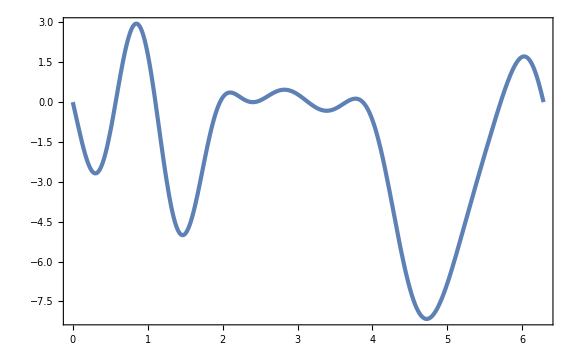

```mathematica
Plot[PcIntegrand[1/2,1,ϕk,-1/2,0,2π/3],{ϕk,0,2π},PlotRange->Full]
```

```mathematica
OGWp[k_]:=2/π^2 k^2 NIntegrate[PpIntegrand[k,q,c3,p3,p2],{q,Abs[k-1],Min[2,k+1]},{c3,-1,1},{p3,0,2π},{p2,0,2π}]
OGWc[k_]:=2/π^2 k^2 NIntegrate[PcIntegrand[k,q,c3,p3,p2],{q,Abs[k-1],Min[2,k+1]},{c3,-1,1},{p3,0,2π},{p2,0,2π},Method->"MonteCarlo"]
```

```mathematica
OGWp[1/2]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -30.4828 and 0.234274 for the integral and error estimates.

{13.3799,-1.54428}